```mathematica
redWin =Image[ -Graphics-];
blueWin =Image[ -Graphics-];
```

```mathematica
IsolaAIv2[col_, row_] := DynamicModule[
{
infinity = 1000,
displayGrid, graphDestroyGrid, displayMatrix, gridX = row, gridY = col, cellSize = 73,destroyMatrix,distanceMatrixRed, distanceMatrixBlue,
moveMatrixRed,moveMatrixBlue, simplerMatrix,displayRedGrid, displayBlueGrid,graphBlueGrid, graphRedGrid,
connectionMatrix,updateConnection,holeMatrix,
updateDistances,
terrainMatrix = 0,floor,
terrainGrid,
gridRules = AssociationThread[{-1, 0, 1, 2, 3}, {"floor1", "void", "floor2", "player1", "player2"}],
playingTurnRules = AssociationThread[{0, 1}, {"blue", "red"}],
playingActionRules = AssociationThread[{0, 1}, {"move", "destroy"}],
getTerrain,
centerX, centerY,
whoIsPlaying = 0, currentAction = 0,
changeTurn, changeAction,
position,
init,
updateMatrix,matrices,
graybtn, redbtn, bluebtn,
allBlueMatrix, allRedMatrix, allBlackMatrix,preMoveMatrixRed,preMoveMatrixBlue,
moveRed, moveBlue, destroyTile, preDestroyMatrix, btnOverlay, checkWin, nullMoveBlue, nullMoveRed,
canBlueMove, canRedMove, UIElement, blueLose, redLose, winScreen,
updateAdjacency, adjacencyMatrix, emptyMatrix, adjacency,
chooseBestMove, possibleMove, possibleMoveBlue,betterMovesBlue,
chooseBestDestroy,possibleDestroy,
moveAI, betterMoves, x, y, smartDestroy, randomDestroy
},
(*variables*)
changeTurn[] := (whoIsPlaying = Mod[whoIsPlaying + 1, 2]);
changeAction[] := (currentAction = Mod[currentAction + 1, 2]);
centerX = Ceiling@(gridX/2);
centerY = Ceiling@(gridY/2);
position = {{centerX, 1}, {centerX, gridY}};
(*functions*)
init[] := (
floor = Table[Table[Mod[i+j, 2], {i,gridX}], {j, gridY}]/.{0-> -1};
terrainMatrix = Table[Table[Mod[i+j, 2], {i,gridY}], {j, gridX}]/.{0-> -1};
terrainMatrix[[position[[1]][[1]],position[[1]][[2]]]] = 2;
terrainMatrix[[position[[2]][[1]],position[[2]][[2]]]] = 3;
allBlueMatrix = Table[Table[bluebtn[j,i], {i, gridY}],{j, gridX}];
allRedMatrix = Table[Table[redbtn[j,i], {i, gridY}],{j, gridX}];
allBlackMatrix = Table[Table[graybtn[j,i], {i, gridY}],{j, gridX}];
(*TESTING FOR OPTI*)
simplerMatrix =terrainMatrix/.{-1|1 -> 0, 0|2|3 -> infinity};
distanceMatrixRed = simplerMatrix + Table[Table[Max[Abs[position[[2, 1]] - j],Abs[position[[2, 2]] - i]], {i, gridX}],{j, gridY}];
distanceMatrixBlue = simplerMatrix+Table[Table[Max[Abs[position[[1, 1]] - j],Abs[position[[1, 2]] - i]], {i, gridY}],{j, gridX}];
preMoveMatrixRed := distanceMatrixRed/.{1-> redbtn[], x_/;x>1 -> Null};
moveMatrixRed := MapThread[MapThread[If[#2===Null,Null,#1]&,{#1,#2}]&,{allRedMatrix,preMoveMatrixRed}];
preMoveMatrixBlue := distanceMatrixBlue/.{1-> bluebtn[],x_/;x>1 -> Null};
moveMatrixBlue := MapThread[MapThread[If[#2===Null,Null,#1]&,{#1,#2}]&,{allBlueMatrix, preMoveMatrixBlue}];
);

init[];

updateMatrix[]:=(
terrainMatrix = floor;
terrainMatrix[[position[[1]][[1]],position[[1]][[2]]]] = 2;
terrainMatrix[[position[[2]][[1]],position[[2]][[2]]]] = 3;
updateDistances[];
matrices[];

updateAdjacency[];

If[currentAction ==0,checkWin[]];
);
(**)
(**)
graybtn[] := Button[Graphics[{Darker[Gray, 0.5], Circle[{0, 0}, 15], Opacity[0.4], Disk[{0, 0}, 15]}], Print["click"], Method->"Queued", ImageSize -> {10, 10}, Appearance->"Frameless"];
bluebtn[] := Button[Graphics[{Darker[Blue, 0.5], Circle[{0, 0}, 15], Opacity[0.4], Disk[{0, 0}, 15]}], Print["click"], Method->"Queued", ImageSize -> {10, 10}, Appearance->"Frameless"];
redbtn[] := Button[Graphics[{Darker[Red, 0.5], Circle[{0, 0}, 15], Opacity[0.4], Disk[{0, 0}, 15]}], Print["click"], Method->"Queued", ImageSize -> {10, 10}, Appearance->"Frameless"];
graybtn[x_, y_] := Button[Graphics[{Darker[Gray, 0.5], Circle[{0, 0}, 15], Opacity[0.4], Disk[{0, 0}, 15]}], destroyTile[x, y], Method->"Queued", ImageSize -> {10, 10}, Appearance->"Frameless"];
bluebtn[x_, y_] := Button[Graphics[{Darker[Blue, 0.5], Circle[{0, 0}, 15], Opacity[0.4], Disk[{0, 0}, 15]}], moveBlue[x, y], Method->"Queued", ImageSize -> {10, 10}, Appearance->"Frameless"];
redbtn[x_,y_] := Button[Graphics[{Darker[Red, 0.5], Circle[{0, 0}, 15], Opacity[0.4], Disk[{0, 0}, 15]}], moveRed[x, y], Method->"Queued", ImageSize -> {10, 10}, Appearance->"Frameless"];
(**)
moveAI[] := (
chooseBestMove[];

chooseBestDestroy[];
);
moveBlue[x_, y_] := (
position[[1]] = {x, y};
updateMatrix[];
changeAction[];
);
destroyTile[x_, y_] := (
floor[[x, y]]=0;
updateMatrix[];
changeTurn[];
changeAction[];
checkWin[];
If[!blueLose &&!redLose,moveAI[];];

);
(**)
(*>>>---AI BEHAVIOUR------------------------*)
chooseBestMove[]:=(
possibleMove = {};
Table[Table[If[preMoveMatrixRed[[j,i]] ===Null, Null, AppendTo[possibleMove, {{j,i}, adjacencyMatrix[[j,i]]}]],{i, gridY}], {j, gridX}];
betterMoves = {};
Table[If[Last[possibleMove[[k]]] ===Max@@Last/@possibleMove, AppendTo[betterMoves, First@possibleMove[[k]]]],{k, Length@possibleMove}];
If[Length@betterMoves == 1, position[[2]] = betterMoves[[1]], position[[2]]=RandomChoice[betterMoves]];
updateMatrix[];
changeAction[];

);
chooseBestDestroy[]:=(
smartDestroy[];

updateMatrix[];
changeTurn[];
changeAction[];
checkWin[];
);

smartDestroy[] := (
updateMatrix[];
possibleMoveBlue = {};
Table[Table[If[preMoveMatrixBlue[[j,i]] ===Null, Null, AppendTo[possibleMoveBlue, {{j,i}, adjacencyMatrix[[j,i]]}]],{i, gridY}], {j, gridX}];
possibleMoveBlue = Select[possibleMoveBlue, First@# != position[[1]]&& First@# != position[[2]]&];
betterMovesBlue = {};
Table[If[Last[possibleMoveBlue[[k]]] ===Max@@Last/@possibleMoveBlue, AppendTo[betterMovesBlue, First@possibleMoveBlue[[k]]]],{k, Length@possibleMoveBlue}];
If[Length@betterMovesBlue == 1, {x, y} = betterMovesBlue[[1]], {x,y} = RandomChoice[betterMovesBlue]];

(*floor[[y, x]] = 0;*)
floor[[x,y]] = 0;
);
(*<<<*)
(*---WIN CONDITION---*)
checkWin[] := (
If[whoIsPlaying == 0,
nullMoveBlue = Cases[moveMatrixBlue, Table[Null, Length[moveMatrixBlue[[1]]]]];
canBlueMove = Length@nullMoveBlue < Length@moveMatrixBlue;
];
If[whoIsPlaying == 1,
nullMoveRed = Cases[moveMatrixRed,Table[Null, Length[moveMatrixRed[[1]]]]];
canRedMove = Length@nullMoveRed < Length@moveMatrixRed;
];

redLose = !canRedMove && whoIsPlaying == 1 && currentAction == 0;
blueLose = !canBlueMove && whoIsPlaying == 0&& currentAction == 0;
UIElement = {redLose, blueLose} /.{{True, False}-> blueWin, {False, True}-> redWin, {False, False} -> {Opacity[0]}};
);
(*<<<*)

(*--------------------------MATRICES----------------------------------------------------*)
matrices[] := (
simplerMatrix :=terrainMatrix/.{-1|1 -> 0, 0|2|3 -> infinity};
terrainGrid := terrainMatrix /.{-1 -> Lighter[Yellow, 0.5],0->Black,1->Lighter[Orange, 0.5],2->Null,3->Null};
If[currentAction==0,
preDestroyMatrix = terrainMatrix/.{-1|1 -> graybtn[], 0|2|3 -> Null};
destroyMatrix = MapThread[MapThread[If[#2===Null,Null,#1]&,{#1,#2}]&,{allBlackMatrix,preDestroyMatrix}]
];

If[currentAction ==1,
If[whoIsPlaying ==0,
preMoveMatrixRed = distanceMatrixRed/.{1-> redbtn[], x_/;x>1 -> Null};
moveMatrixRed = MapThread[MapThread[If[#2===Null,Null,#1]&,{#1,#2}]&,{allRedMatrix,preMoveMatrixRed}],
preMoveMatrixBlue = distanceMatrixBlue/.{1-> bluebtn[],x_/;x>1 -> Null};
moveMatrixBlue = MapThread[MapThread[If[#2===Null,Null,#1]&,{#1,#2}]&,{allBlueMatrix, preMoveMatrixBlue}];
];
];
);
(**)
updateConnection[] :=(
holeMatrix =terrainMatrix/.{-1|1|2|3 -> 0,  0-> -infinity};
);
(**)

updateDistances[] := (
simplerMatrix =terrainMatrix/.{-1|1 -> 0, 0|2|3 -> infinity};
If[whoIsPlaying ==0,
distanceMatrixRed = simplerMatrix + Table[Table[Max[Abs[position[[2, 1]] - j],Abs[position[[2, 2]] - i]], {i, gridY}],{j, gridX}],
distanceMatrixBlue = simplerMatrix+Table[Table[Max[Abs[position[[1, 1]] - j],Abs[position[[1, 2]] - i]], {i, gridY}],{j, gridX}];
];
);

updateAdjacency[]:=(
emptyMatrix = simplerMatrix/.{0 -> 1, infinity ->0};
adjacencyMatrix = Table[
Table[
Total@Flatten@Table[
Table[
If[ii>0&&ii<=Length@emptyMatrix &&jj>0&&jj<=Length@emptyMatrix,
emptyMatrix[[jj, ii]],
0], 
{ii, i-1, i+1}], 
{jj, j-1,j+1}] - emptyMatrix[[j, i]],
{i, gridY}], 
{j,gridX}];
);
(*<<<--------------------------<<<*)

displayGrid[] := Grid[terrainGrid, Frame->None,  Alignment->{Center, Center}, ItemSize->{5, 5}];
displayBlueGrid[] := Grid[distanceMatrixBlue, Frame->None,  Alignment->{Center, Center}, ItemSize->{5, 5}];
displayRedGrid[] := Grid[distanceMatrixRed, Frame->None,  Alignment->{Center, Center}, ItemSize->{5, 5}];
adjacency[] := GraphicsGrid[adjacencyMatrix, 
Frame->None,  Alignment->{Center, Center}, 
ItemAspectRatio->1 (*ImageSize-> {gridX*cellSize, gridY * cellSize}*)
];
graphDestroyGrid[] := GraphicsGrid[destroyMatrix, 
Frame->None,  Alignment->{Center, Center}, 
ItemAspectRatio->1 (*ImageSize-> {gridX*cellSize, gridY * cellSize}*)
];
graphRedGrid[] := GraphicsGrid[moveMatrixRed, 
Frame->None,  Alignment->{Center, Center}, 
ItemAspectRatio->1 (*ImageSize-> {gridX*cellSize, gridY * cellSize}*)
];
graphBlueGrid[] := GraphicsGrid[moveMatrixBlue, 
Frame->None,  Alignment->{Center, Center}, 
ItemAspectRatio->1 (*ImageSize-> {gridX*cellSize, gridY * cellSize}*)
];
btnOverlay[] := {whoIsPlaying, currentAction}/.{{0,1}->graphDestroyGrid[], {0, 0} -> graphBlueGrid[], {1, _} -> Graphics[]};
displayMatrix[] := MatrixPlot[terrainMatrix, Frame->None, ColorRules->{-1 -> Lighter[Yellow, 0.5],0->Black,1->Lighter[Orange, 0.5],2->Blue,3->Red}, Background->LightBlue];
winScreen[] := Graphics[{UIElement }];

(*position[[1, 1]] = 2;
position[[2, 1]] = 4;
position[[2, 2]] = 3;
floor[[3, 3]] = 0;
floor[[3, 2]] = 0;
*)
updateMatrix[];

Dynamic@Overlay[{displayMatrix[], btnOverlay[], winScreen[]}, None, 2]
]; 
IsolaAIv2[4, 4]
```

{{1,1,1},{1,1,1},{1,1,1}}

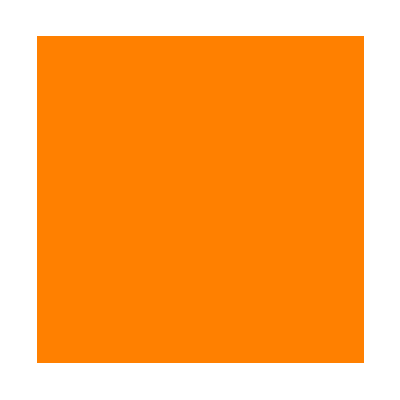
-Graphics-4 | 6 | 4
6 | 9 | 6
4 | 6 | 4

```mathematica
matrix={{0, 0, 0}, {0, 0, 0}, {0, 0, 0}};
connections=matrix/.{0->1, 1->Null};
Print[connections];
connections = Table[Table[If[connections[[i, j]]===Null,Null,Total@Flatten@Table[Table[If[connections[[ii, jj]]===Null, 0, connections[[ii, jj]]], {jj, Max[j-1, 1], Min[j+1,Length@connections[[i]]]}], {ii, Max[i-1, 1], Min[i+1, Length@connections]}]], {j,Length@connections[[i]]}], {i, Length@connections}];
Overlay[{MatrixPlot[matrix, ColorRules->{0->Orange, 1->Blue}, Frame->None],Grid[connections, Frame->None, ItemSize->{8,8}] }]
```